```mathematica
fww=1;
p=1;
d=0;
```

```mathematica
yww=1/3;
ywd=1/3;
ydd=1/3;
xww=1/3;
xwd=1/3;
xdd=1/3;
```

```mathematica
fddoverc={};
For[c=0,c≤0.5,c=c+0.1,
fddoverr={};
For[r=1,r≤10,r++,
fwd=1-c;
fdd=(1-c)^2;
(*Fww=r (fdd xdd+fwd xwd+fww xww)^((-1)+r) ((-1) fwd ((-1)+p) xwd+fww xww) (((-1)+d) fwd ((-1)+p) xwd+fww xww);
Fwd=r (fdd xdd+fwd xwd+fww xww)^((-1)+r) ((-1) fwd ((-1)+p) ( 2 fdd xdd xwd+2 fwd p xwd^2)+fww (2 fdd xdd xww+2 fwd p xwd xww));*)
Fdd=r (fdd xdd+fwd p xwd)^2 (fdd xdd+fwd xwd+fww xww)^((-1)+ r);
AppendTo[fddoverr,{r,Fdd}]
];
AppendTo[fddoverc,fddoverr]
]
```

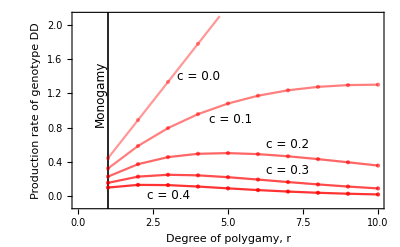

```mathematica
ListPlot[fddoverc⟦{1,2,3,4,5}⟧,Joined->True,PlotRange->{Automatic,{-0.1,2.1}},Frame->True,FrameStyle->Directive[Black,Thickness[0.002]],Mesh->True,MeshStyle->Directive[PointSize[Medium]],PlotStyle->{Directive[Red,Opacity[0.4]],Directive[Red,Opacity[0.5]],Directive[Red,Opacity[0.6]],Directive[Red,Opacity[0.7]],Directive[Red,Opacity[0.8]],Directive[Red,Opacity[0.9]]},Epilog->{Inset[Style["c = 0.0",12],{4,1.4}],Inset[Style["c = 0.1",12],{5.1,0.9}],
Inset[Style["c = 0.2",12],{7,0.6}],
Inset[Style["c = 0.3",12],{7,0.3}],
Inset[Style["c = 0.4",12],{3,0.01}],
Inset[Style[Rotate["Monogamy",90 Degree],12],{0.75,1.2}]},FrameLabel->{Style["Degree of polygamy, r",Black,16],Style["Production rate of genotype DD",Black,16]},FrameStyle->Directive[Black,Thickness[0.003]],GridLines->{{1},None},GridLinesStyle->Directive[Black,Thickness[0.003]]]
```

```mathematica
data=Table[fwd=1-c;
fdd=(1-c)^2;(r (fdd xdd+fwd p xwd)^2 (fdd xdd+fwd xwd+fww xww)^((-1)+ r)),{c,0,0.2,0.01},{r,1,20,1}];
```

```mathematica
ListDensityPlot[data,ColorFunction->(Directive[Red,Opacity[#]]&)]
```

-Graphics-